# Tools for Complex

## Plots

```mathematica
ComplexPlot3D[Exp[z],{z,π},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:= Sin[z^2]/((1+z^2)^2)
g[z_]:= √(1+z^2)
ComplexPlot3D[f[z],{z,2},PlotLegends->Automatic]
ComplexPlot3D[g[z],{z,2},PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

```mathematica
h[z_]:=√(z+ⅈ)
ComplexPlot3D[h[z],{z,2},PlotLegends->Automatic]
```

-Graphics3D-

## Parameterizations

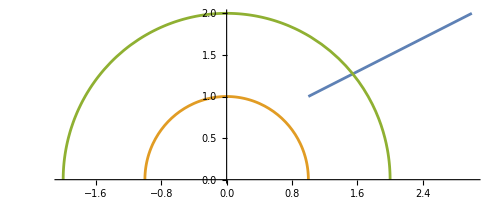

```mathematica
Clear[z1,z2,t,a,b]
z1[t_]:= 1+ⅈ + t (2 +ⅈ)
z2[t_]:= ⅇ^(π  ⅈ t)
z3[t_]:= 2 ⅇ^(π  ⅈ t^2)
ParametricPlot[{
ReIm[z1[t]],
ReIm[z2[t]],
ReIm[z3[t]]},{t,0, 1}]
```

## Mappings

### f(z)=z^2

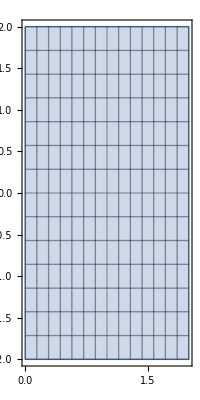
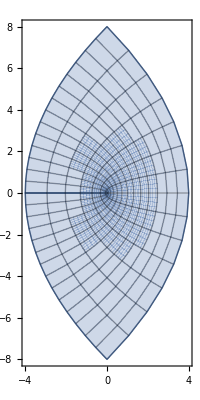
{-Graphics-,⟶,-Graphics-}

```mathematica
f[z_]:= z^2
{ParametricPlot[ReIm[x+ I y],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[x+ I y]],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All]}
```

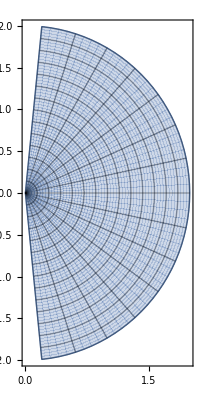
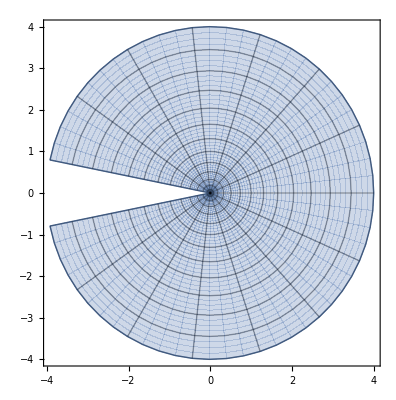
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π/2+0.1,π/2-0.1},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π/2+0.1,π/2-0.1},
Mesh->Full,
PlotRange->All]}
```

### f(z)=z^(1/2)

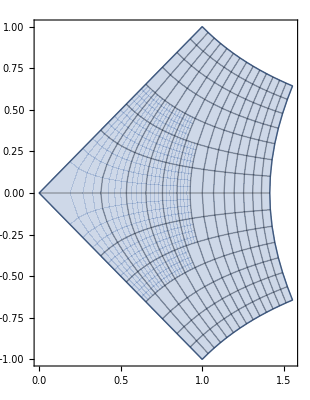
{-Graphics-,⟶,-Graphics-}

```mathematica
f[z_]:= z^(1/2)
{ParametricPlot[ReIm[x+ I y],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[x+ I y]],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All]}
```

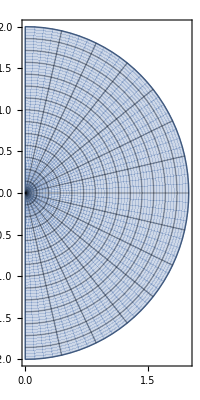
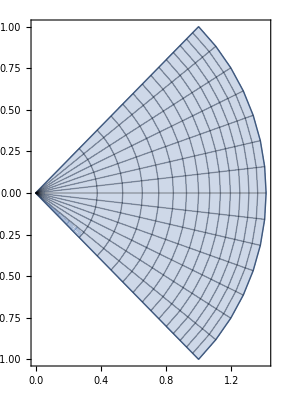
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
PlotRange->All]}
```

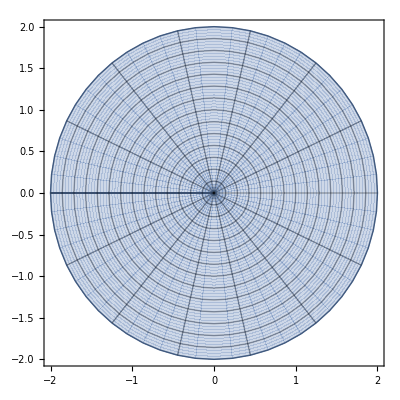
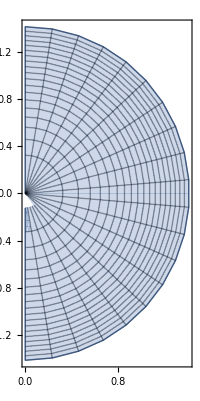
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π,π},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π,π},
Mesh->Full,
PlotPoints->20,
PlotRange->All]}
```

### f(z)=a z+ b

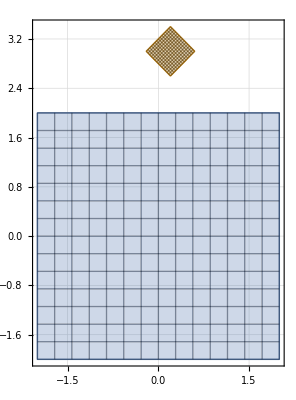

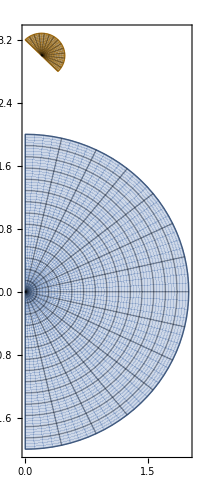

-Graphics3D-

```mathematica
a=0.1+0.1 ⅈ;
b=0.2+3ⅈ;
f[z_]:=a z + b 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,-2,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,10},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}
]
```

### f(z)=ⅇ^z

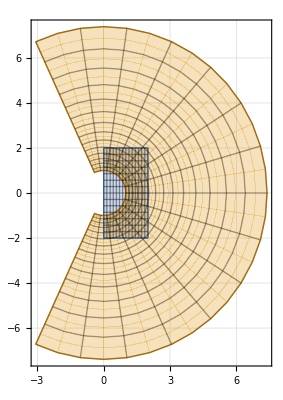

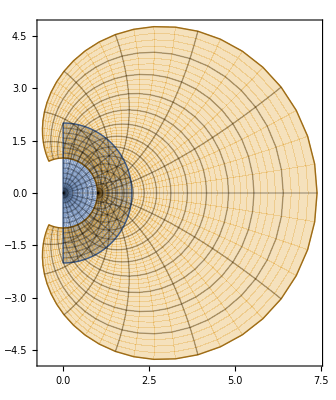

-Graphics3D-

```mathematica
f[z_]:=ⅇ^z 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=Log[z]

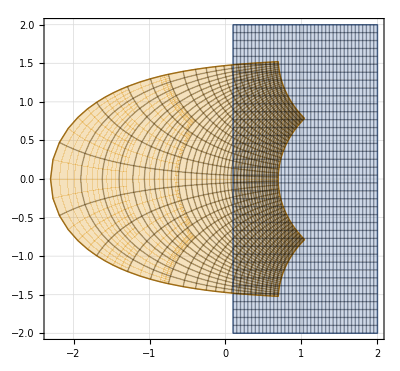

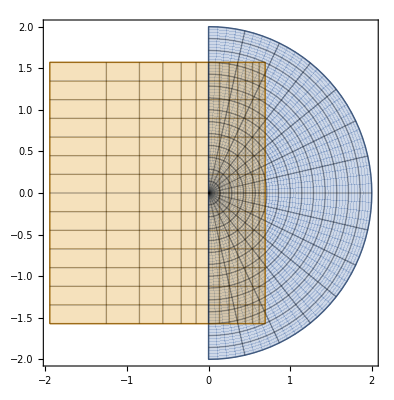

-Graphics3D-

```mathematica
f[z_]:=Log[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotPoints->40,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=Sin[z]

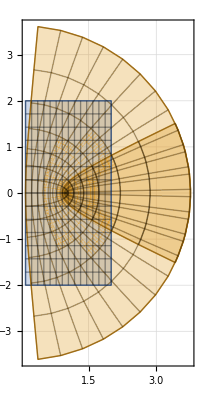

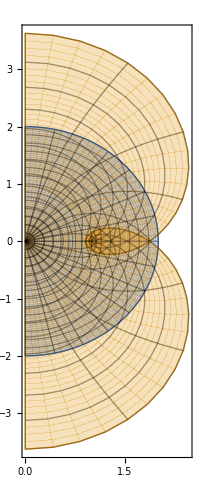

-Graphics3D-

```mathematica
f[z_]:=Sin[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=ArcSin[z]

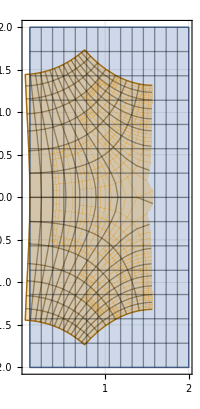

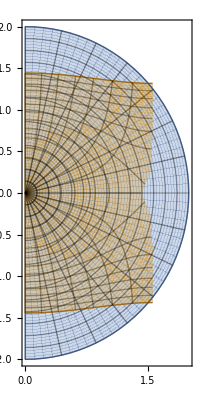

-Graphics3D-

```mathematica
f[z_]:=ArcSin[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=Tan[z]

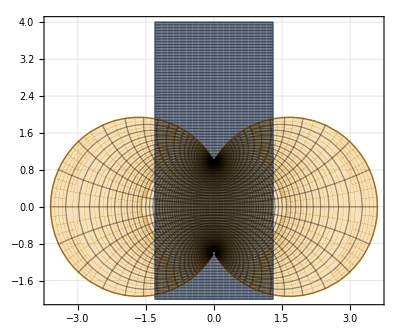

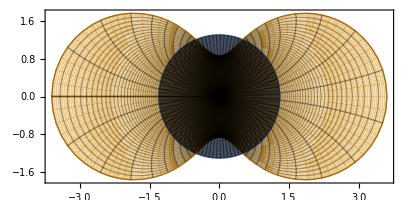

-Graphics3D-

```mathematica
f[z_]:=Tan[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,-1.3,1.3},{y,-2,4},
Mesh->Full,
PlotPoints->100,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,1.3},{θ,-π,π},
Mesh->Full,
PlotPoints->100,
AspectRatio->Automatic,
PlotRange->All]
ComplexPlot3D[f[z],{z,4},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]
```

### f(z)=ArcTan[z]

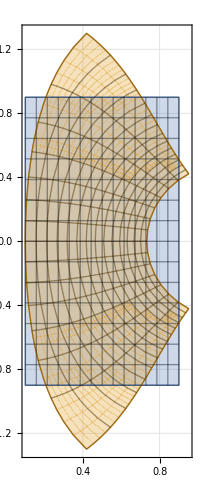

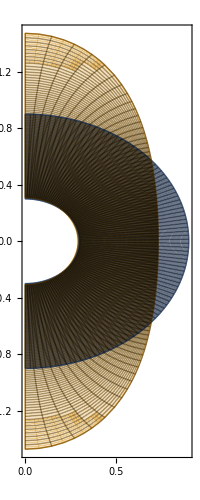

-Graphics3D-

{-Graphics3D-,-Graphics3D-}

```mathematica
f[z_]:=ArcTan[z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,0.9},{y,-0.9,0.9},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0.3,0.9},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All,
PlotPoints->100]
ComplexPlot3D[f[z],{z,4},
PlotLegends->Automatic,
PlotRange->{0,2},
AxesLabel->{"re","im","Abs[f[z]]"}]

{ComplexPlot3D[z,{z,0.5},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}],
ComplexPlot3D[f[z],{z,0.5},
PlotLegends->Automatic,
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]}
```

```mathematica
R=0.8
{ComplexPlot3D[z,{z,R},
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}],
ComplexPlot3D[f[z],{z,R},
PlotLegends->Automatic,
PlotLegends->Automatic,
AxesLabel->{"re","im","Abs[f[z]]"}]}
```

0.8

{-Graphics3D-,-Graphics3D-}

### f(z)=EulerPhi[z]

```mathematica
BesselJ[0, 1.0 + I]
```

0.937608-0.49653 ⅈ

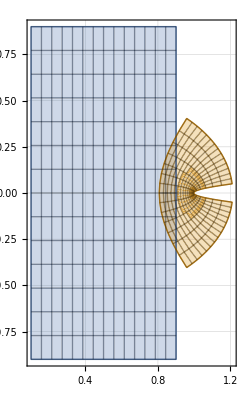

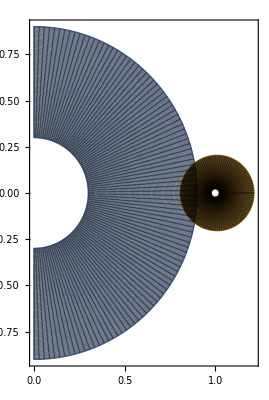

-Graphics3D-

```mathematica
f[z_]:=BesselJ[0,z] 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0.1,0.9},{y,-0.9,0.9},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0.3,0.9},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All,
PlotPoints->100]
ComplexPlot3D[f[z],{z,4},
PlotLegends->Automatic,
PlotRange->{0,2},
AxesLabel->{"re","im","Abs[f[z]]"}]
```